## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/a-fe/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/a-fe

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 11.3356 | 0.135415
1000. | 0. | 24.3584 | 0.199192
2000. | 0. | 51.3311 | 0.295858
3000. | 0. | 77.3608 | 0.357353
4000. | 0. | 105.193 | 0.39868
5000. | 0. | 131.523 | 0.448576
6000. | 0. | 157.394 | 0.493261
7000. | 0. | 185.215 | 0.522367
8000. | 0. | 211.818 | 0.582709
9000. | 0. | 237.393 | 0.612214
10000. | 0. | 263.437 | 0.654697

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-2.49549+0.0269686 x-3.36172×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.49549 | 0.458877 | -5.43824 | 0.000617263
x | 0.0269686 | 0.000212355 | 126.998 | 1.65223×10^-14
x^2 | -3.36172×10^-8 | 2.00189×10^-8 | -1.67927 | 0.131614

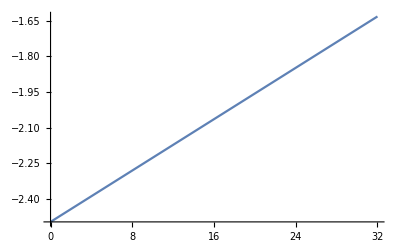

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
```

{0.355174,-0.0810907,0.023783,-0.74704,0.351493,0.0154758,-0.712382,0.577439,0.715877,-0.106193,-0.392535}

{0.135415,0.199192,0.295858,0.357353,0.39868,0.448576,0.493261,0.522367,0.582709,0.612214,0.654697}

{6.87933,0.165729,0.006462,4.37012,0.777289,0.00119025,2.0858,1.22197,1.50929,0.0300873,0.359481}

```mathematica
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

2.17584

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

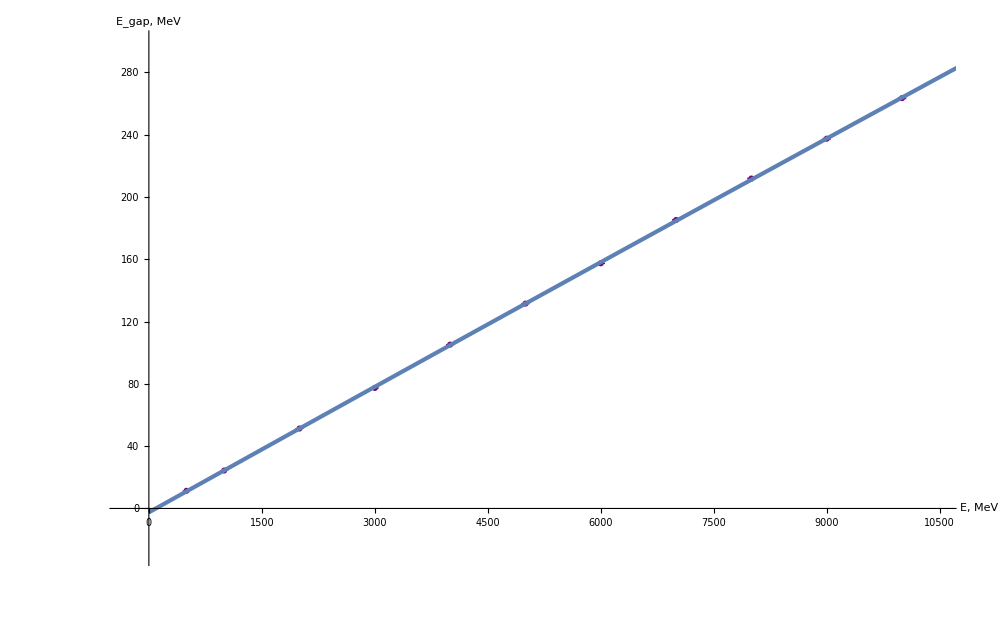

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,300}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-2.49549,0.0269686,-3.36172×10^-8},{0.458877,0.000212355,2.00189×10^-8},2.17584}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
874.735 | 9.35857 | 0.255107 | 0.00555725
1370.45 | 11.3654 | 0.198488 | 0.00401328
1957.69 | 13.6568 | 0.168017 | 0.00330892
2925.84 | 16.0486 | 0.143458 | 0.00274768
3535.59 | 18.3884 | 0.126563 | 0.00241018
4073.64 | 19.7814 | 0.123685 | 0.00235984
4982.27 | 22.1418 | 0.109259 | 0.00205822
6372.49 | 26.5174 | 0.0987407 | 0.00184961
7106.15 | 27.0694 | 0.0934535 | 0.00175847
7998.51 | 28.1291 | 0.0865724 | 0.0016144
9739.03 | 31.0072 | 0.0816041 | 0.00151679

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00738885+7.22538/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00738885 | 0.00211958 | 3.48599 | 0.00687336
1/(√x) | 7.22538 | 0.111433 | 64.8408 | 2.49137×10^-13

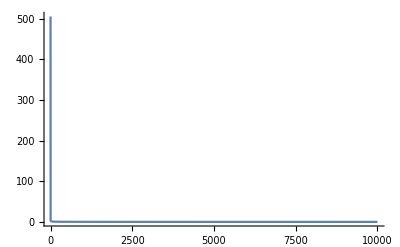

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
```

{0.00341826,-0.00407754,-0.00267258,0.00249135,-0.00234081,0.00309015,-0.000494318,0.000839812,0.000352205,-0.00160627,0.000999728}

{0.00555725,0.00401328,0.00330892,0.00274768,0.00241018,0.00235984,0.00205822,0.00184961,0.00175847,0.0016144,0.00151679}

{0.378348,1.03228,0.652364,0.822123,0.943261,1.71473,0.0576807,0.20616,0.0401162,0.989945,0.43442}

```mathematica
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

0.807936

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

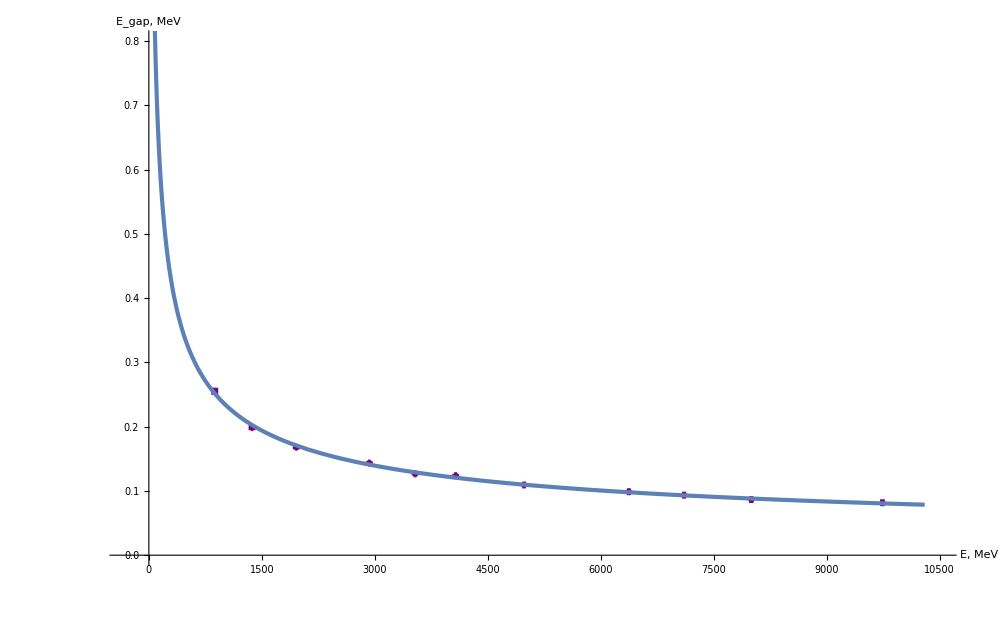

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.8}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00738885,7.22538},{0.00211958,0.111433},0.807936}

fit_re_res.csv